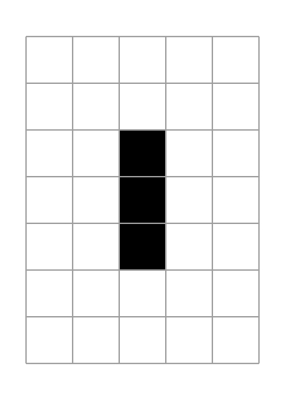
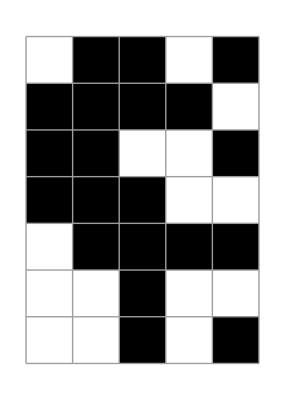
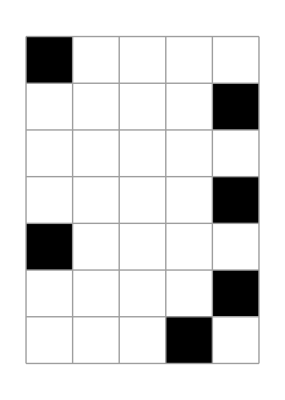
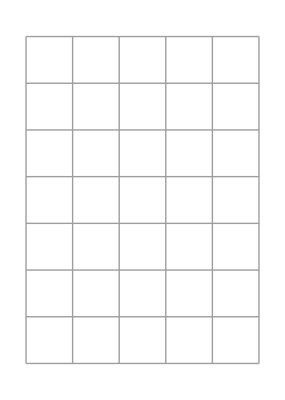
{0.06436,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
endState=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
endGeneration=4;
Get[NotebookDirectory[]<>"wordLife.m"]
```

```mathematica
beforeCNF
```

1
 |  |  |  |

```mathematica
S[i_,j_,g_]:=Union[R1[i,j,g],R2[i,j,g],R3[i,j,g],R4[i,j,g]];
cnf2clausalForm2[
BooleanConvert[clausalForm22cnf[S[i,j,g]] ,"CNF"]
 ]
```

{{!x[6,4,g],!x[6,5,g],!x[6,6,g],!x[7,4,g],x[7,5,g],!x[7,5,1+g]},258,{!x[7,4,g],x[7,5,g],!x[7,5,1+g],!x[7,6,g],!x[8,4,g],!x[8,5,g]}}
 |  |  |  |

```mathematica
beforeCNF=(array3Processor@Array[S,{i,j,n-1}]);
```